{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97}

9

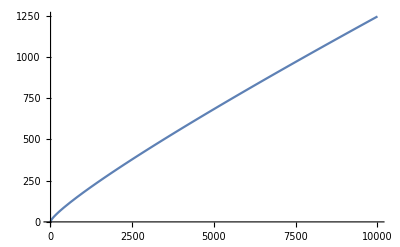

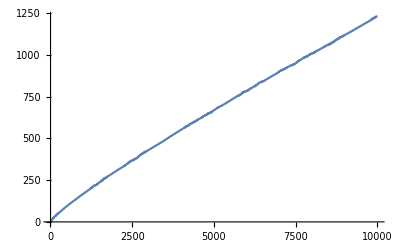

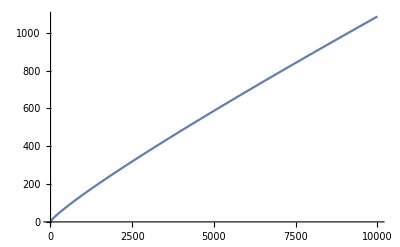

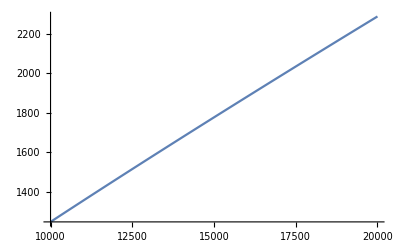

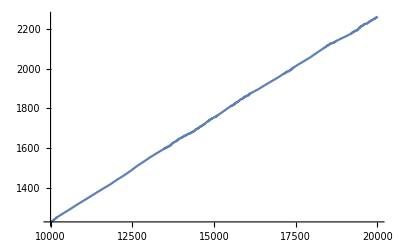

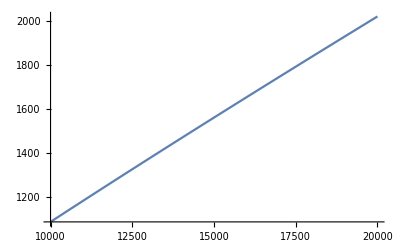

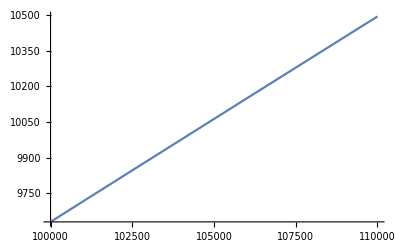

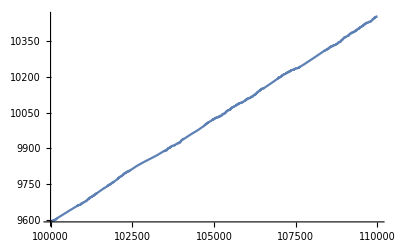

{{5,3},{7,5},{13,11},{19,17},{31,29},{43,41},{61,59},{73,71},{103,101},{109,107},{139,137},{151,149},{181,179},{193,191},{199,197},{229,227}}

We have: 16 pairs of twin primes within the range of: 250

{{5,3},{7,5},{13,11},{19,17},{31,29},{43,41},{61,59},{73,71},{103,101},{109,107},{139,137},{151,149},{181,179},{193,191},{199,197},{229,227}}

Our Wilson Primes within 1000 are: {5,13,563}

{5,13,563}

b= 235, Mod[b^(n-1),n]= 91, holds = False

```mathematica
(*Problem 1: The list of prime numbers within the range of n
 will be found through this implementation of the Sieve
of Erastosthenes and constantly removing non prime numbers
within our initial list of numbers.*)
SieveOfEratosthenes[n_]:=Module[{numbers=Range[n],plist={}},
Do[
If[numbers[[i]]≠0,
Do[numbers[[i*j]]=0,
{j,2,n/i}]],
{i,2,Sqrt[n]}];
plist =Select[numbers,#>1&];
Return[plist]
]

SieveOfEratosthenes[100]


(*Problem 2: Plotting pi(x), Li(x),x/ln(x) within ranges: 2≤x≤10000, 10000≤x≤20000, 100000≤x≤110000 *)
(*Defining π(x) below:*)
PrimeCt[x_]:=Module[{count,plist},
plist = SieveOfEratosthenes[x];
count = Length[plist];
Return[count]
]

PrimeCt[25]

(*Plotting all 3 functions below with their respective legends and given ranges.*)
(*2≤x≤10000*)
Plot[LogIntegral[x],{x,2,10000},PlotLegends -> "Li[x]"]
Plot[PrimeCt[x],{x,2,10000},PlotLegends -> "π[x]"]
Plot[x/Log[x],{x,2,10000},PlotLegends -> "x/Log[x]"]

(*10000≤x≤20000*)
Plot[LogIntegral[x],{x,10000,20000},PlotLegends -> "Li[x]"]
Plot[PrimeCt[x],{x,10000,20000},PlotLegends -> "π[x]"]
Plot[x/Log[x],{x,10000,20000},PlotLegends -> "x/Log[x]"]

(*100000≤x≤110000*)
Plot[LogIntegral[x],{x,100000,110000},PlotLegends -> "Li[x]"]
Plot[PrimeCt[x],{x,100000,110000},PlotLegends -> "π[x]"]
Plot[x/Log[x],{x,100000,110000},PlotLegends -> "x/Log[x]"]


(*Problem 3: Determining the amount of twin primes within a range
If two prime numbers have a difference of two between them, 
  i.e 3 and 5, then they are defined to be a set of twin primes.*)
Twinprimes[range_]:=Module[{plist={},i,twinlist={}},
plist = SieveOfEratosthenes[range];

For[i=1,i<Length[plist]-1,i++,
If[plist[[i+1]]-plist[[i]]==2, AppendTo[twinlist,{plist[[i+1]],plist[[i]]}]];

]


Print[twinlist];
Print[StringForm["We have: `` pairs of twin primes within the range of: ``",Length[twinlist],range]];
Return[twinlist]
]

Twinprimes[250]



(*Problem 4: Wilson Prime Generator 
A Wilson prime is a prime number p 
such that: (p-1)! =-1(mod p).*)
WilsonPrimes[plist_,N_]:= Module[{prime,i,wlist={}},

For[i=1,i≤Length[plist],i++,
prime = plist[[i]];
If[Mod[((prime-1)!+1),prime^2]==0, AppendTo[wlist,prime]];
]
Print[StringForm["Our Wilson Primes within `` are: ``",N,wlist]];
Return[wlist]
]

WilsonPrimes[SieveOfEratosthenes[1000],1000]


(*Problem 5: This function will check if b^(n-1)=1 (mod n)
for a random integer b between 2 and n-1.*)

prob5[n_]:=Module[{b,holds=False},
b = RandomInteger[{2,n-1}];
If[Mod[b^(n-1),n]==1, holds = True];
Print[StringForm["b= ``, Mod[b^(n-1),n]= ``, holds = ``",b,Mod[b^(n-1),n],holds]]
]

prob5[666]
```